21

21

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

Piecewise[{{(0.0830558 (-3+((2+1.73395×10^-20 R^2) Log[(7.59419×10^9 (1+√(1-1.73395×10^-20 R^2)))/R])/(√(1-1.73395×10^-20 R^2))))/((1-1.73395×10^-20 R^2)^2), R<7.59419×10^9}, {0.0221482, R==7.59419×10^9}, {(0.0830558 (-3+((2+1.73395×10^-20 R^2) ArcCos[(7.59419×10^9)/R])/(√(-1+1.73395×10^-20 R^2))))/((1-1.73395×10^-20 R^2)^2), R>7.59419×10^9}, {0, True}}]

| Estimate | Standard Error | t-Statistic | P-Value
M | 1400.11 | 0. | ∞ | 0.
a | 7.59419×10^9 | 4.56308×10^-45 | 1.66427×10^54 | 3.83457179040951×10^-966
gamma | 4.6521×10^-17 | 3.80823×10^-19 | 122.159 | 9.92155×10^-28

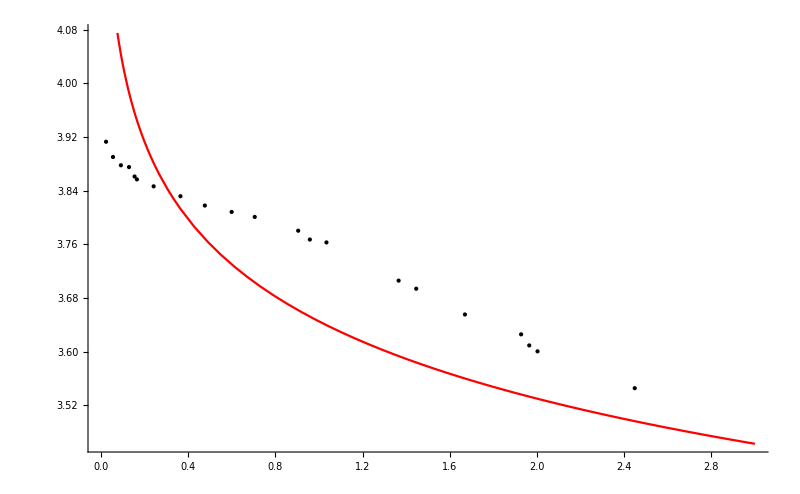

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["I_R_surf_arcmin.dat"];
L=Length[data]
21
(*M = 1.4;
a = 1.2;
gamma =1.0;*)
Ip[R_]:=Piecewise[{{M*((2+(R/a)^2)*(Log[(1+Sqrt[1-(R/a)^2])/(R/a)]/(Sqrt[1-(R/a)^2]))-3)/(2*Pi*a^2*gamma*(1-(R/a)^2)^2),R<a},{
2*M/(15*Pi*a^2*gamma),R==a},{
M*((2+(R/a)^2)*(ArcCos[1/(R/a)]/Sqrt[(R/a)^2-1])-3)/(2*Pi*a^2*gamma*(1-(R/a)^2)^2),R>a}}];
(*Plot[Ip[R],{R,0,5}]*)

fit = NonlinearModelFit[data,Ip[R],{M,a,gamma},R,MaxIterations->1000];
fit["BestFit"]
fit["ParameterTable"]
Plot[fit[R],{R,0,3},PlotStyle->Red,Epilog:>Point[data],ImageSize->800]
```